```mathematica
(*Preceptron*)
```

```mathematica
sampledata=RandomVariate[UniformDistribution[{{0,5},{0,5}}],10];
```

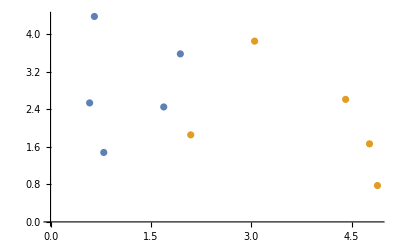

```mathematica
wbar =2;
bbar = -2;

truedata = Select[sampledata,#[[2]]>= wbar*#[[1]]+bbar&];
falsedata = Select[sampledata,#[[2]]< wbar*#[[1]]+bbar&];Show[ListPlot[{truedata,falsedata}]]
```

```mathematica
(*Preceptron Model*)
```

```mathematica
MisclassifedQ[data_,w_,b_]:=If[MemberQ[truedata,data],1,-1]*(Inner[Times,Flatten[w],{data[[1]],data[[2]]}]+b);
```

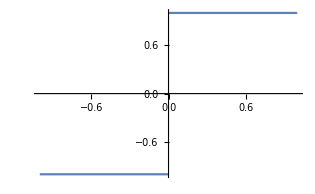

```mathematica
Plot[Sign[x],{x,-1,1}] (*感知机的输入输出*)
```

```mathematica
(*Preceptron Algoritm*)
Preceptron[η_,truedata_,falsedata_]:=Module[{},
w={RandomReal[],RandomReal[]};
b=RandomReal[];
dataset=Riffle[truedata,falsedata];
k=1;
While[!FreeQ[MisclassifedQ[#,w,b]<=0&/@dataset,True],
data=dataset[[FirstPosition[MisclassifedQ[#,w,b]<=0&/@dataset,True]]][[1]];

w=w+(η)*data*If[MemberQ[truedata,data],1,-1];
b=b+(η)*If[MemberQ[truedata,data],1,-1];
k=k+1;
];
Print["w:",MatrixForm[w],"  b:",MatrixForm[b],"   Times:",k]
];
PreceptronClassifier[data_]:=Module[{},
{data[[1]],data[[2]],Sign[Sign[Inner[Times,w,{data[[1]],data[[2]]}]+b]]}
];
```

w:(-0.342042
0.209007)  b:0.163989   Times:27

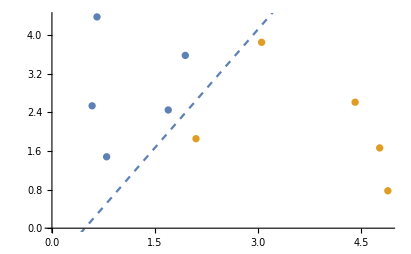
{-Graphics3D-,-Graphics-}

```mathematica
Preceptron[0.01,truedata,falsedata];
{Show[Plot3D[Sign[Inner[Times,w,{x1,x2}]+b],{x1,0,5},{x2,0,5},Mesh->None,PlotStyle->Opacity[0.3],ColorFunction->"TemperatureMap"],ListPointPlot3D[{PreceptronClassifier[#]&/@truedata,PreceptronClassifier[#]&/@falsedata}]],Show[ListPlot[{truedata,falsedata}],Plot[-(w[[1]]*x+b)/w[[2]],{x,0,5},PlotStyle->Dashed]]}
```